# Preliminaries

```mathematica
nMax[pars_]:=Ceiling[1.2((-1+s+r0 s) γ0)/(r0 s)/.pars]/.pars
```

```mathematica
e[i1_,i2_,pars_]:=(i1-1)(nMax[pars])+i2
```

```mathematica
test={r0->0.2,γ0->10,s->0.95,σ->0.00,β->1};
```

```mathematica
s>1/(1+r0)/.test
```

True

```mathematica
tmaxN=100 ; ΔtN=5;
tmaxP=500;ΔtP=10;
```

### Initial vector

```mathematica
vec0[pars_,n0_]:=Block[{out,i1,i2},out={};
For[i1=1,i1≤nMax[pars],i1++,
For[i2=1,i2≤ nMax[pars],i2++,
If[i1==n0[[1]]&&i2==n0[[2]],AppendTo[out,1],AppendTo[out,0]];
]
];
out//N
]
```

### vector to matrix

```mathematica
v2m[pars_,vIn_]:=Block[{out2,i1,i2,ct},out2=Table[0,{i1,1,nMax[pars]},{i2,1,nMax[pars]}];ct=1;
For[i1=1,i1≤nMax[pars],i1++,
For[i2=1,i2≤nMax[pars],i2++,
out2[[i1,i2]]=vIn[[ct]];
ct++;
];
];
out2
]
```

# The Ecological model

## Deterministic population dynamics

```mathematica
n1=n(1+r0 (1-n/γ0))s;
```

```mathematica
Δn=n1-n//Factor;
```

## Equilibria-Exact

```mathematica
Δn
```

-(n (n r0 s+γ0-s γ0-r0 s γ0))/γ0

```mathematica
equi=Solve[Δn==0,n]//Simplify
```

{{n→0},{n→((-1+s+r0 s) γ0)/(r0 s)}}

### Biological validity

```mathematica
Reduce[{(n/.equi[[1]])>0,0<γ,0<s<1,0<r}]//Simplify
```

False

```mathematica
Reduce[{(n/.equi[[2]])>0,0<γ0,0<s<1,0<r0}]//FullSimplify
```

r0>0&&γ0>0&&s+r0 s>1&&s<1

### Stability

```mathematica
slope=Simplify[D[Δn,n]/.equi[[2]]]
```

1-(1+r0) s

```mathematica
Reduce[{slope<0,0<γ0,0<s<1,0<r0}]//Simplify
```

γ0>0&&r0>0&&s+r0 s>1&&s<1

Equilibrium 2 is always valid and stable

## Numerical dynamics

```mathematica
Clear[nEco]
nEco[pars_,tmax_,n0_]:=Block[{out,t},out={{0,n0}};
For[t=1,t≤tmax,t++,
AppendTo[out,{t,n1/.pars/.n->out[[t,2]]}]
];
out
]
```

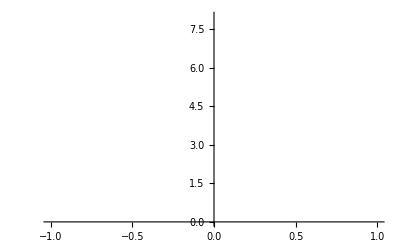

```mathematica
ListLinePlot[nEco[test,tMaxN,4],PlotStyle->Black,PlotRange->All]
```

## Stochastic dynamics

### Initial vector

```mathematica
nInit[pars_,n0_]:=Table[If[i==n0,1,0],{i,1,nMax[pars]}]
```

```mathematica
nInit[test,4]
```

{0,0,0,1,0,0,0,0,0}

### Transition matrix

```mathematica
Clear[BMtrx]
```

```mathematica
BMtrx[pars_]:=Block[{out,i,j,λ},out={};
out=Table[0,{j,1,nMax[pars]},{i,1,nMax[pars]}];
For[j=1,j≤nMax[pars],++j,
For[i=1,i ≤ nMax[pars],++i,
λ=i r0(1-i/γ0)/.pars;
If[j≥i&&λ>0,
out[[j,i]]=PDF[TruncatedDistribution[{-1,nMax[pars]-i},PoissonDistribution[λ]],j-i]
];
]];
For[j=1,j≤nMax[pars],++j,
out[[j,j]]+=1-Total[out[[;;,j]]];
];
out
]
```

```mathematica
DMtrx[pars_]:=Block[{out,i,j},
out=Table[0,{j,1,nMax[pars]},{i,1,nMax[pars]}];
For[i=1,i ≤ nMax[pars],++i,
For[j=1,j≤nMax[pars],++j,
If[j≤i,
out[[j,i]]=PDF[BinomialDistribution[i,s/.pars],j];
]
]
];
For[i=1,i≤nMax[pars],i++,
out[[1,i]]+=PDF[BinomialDistribution[i,s],0]/.pars
];
out//Chop
]
```

```mathematica
Clear[TMtrx]
TMtrx[pars_]:=TMtrx[pars]=DMtrx[pars].BMtrx[pars]//Chop
```

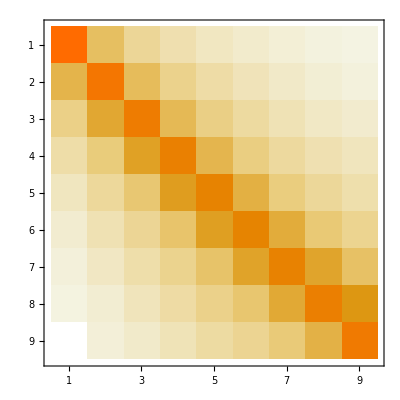

```mathematica
TMtrx[test]//MatrixPlot
```

### Dynamics

```mathematica
state[pars_,n0_,t_]:=MatrixPower[TMtrx[pars],t].nInit[pars,n0]
```

```mathematica
Transpose[Table[Reverse[state[test,4,i]],{i,0,tMaxN,ΔtN}]]//MatrixPlot
```

Table::iterb: Iterator {i,0,tMaxN,5} does not have appropriate bounds.

MatrixPlot::mat0: Argument Transpose[Table[Reverse[state[test,4,i]],{i,0,tMaxN,5}]] at position 1 is not a matrix.

MatrixPlot[Transpose[Table[Reverse[state[test,4,i]],{i,0,tMaxN,5}]]]

```mathematica
distPlot1=MatrixPlot[Transpose[Table[0.5-Reverse[state[test,4,i]],{i,0,tMaxN,ΔtN}]],ColorFunction->"GrayTones",FrameTicks->{Table[{i,ToString[nMax[test]-i+1]},{i,0,nMax[test],2}],Table[{i,ToString[(i-1) ΔtN]},{i,1,tMaxN/ΔtN+1,5}],False,False}];
```

Table::iterb: Iterator {i,0,tMaxN,5} does not have appropriate bounds.

Table::iterb: Iterator {i,1,1+tMaxN/5,5} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

MatrixPlot::mat0: Argument Transpose[Table[0.5-Reverse[state[test,4,i]],{i,0,tMaxN,5}]] at position 1 is not a matrix.

```mathematica
meanPlot1=ListLinePlot[Transpose[{Table[g/ΔtN,{g,0,tMaxN,ΔtN}],Table[state[test,4,g],{g,0,tMaxN,ΔtN}].Table[i,{i,1,nMax[test]}]}],PlotStyle->Red,PlotRange->All];
```

Table::iterb: Iterator {g,0,tMaxN,5} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Table[g/ΔtN,{g,0,tMaxN,5}],Table[state[test,4,g],{g,0,tMaxN,5}].{1,2,3,4,5,6,7,8,9}} cannot be transposed.

Transpose::nmtx: The first two levels of {Table[g/ΔtN,{g,0,tMaxN,5.}],Table[state[test,4.,g],{g,0,tMaxN,5.}].{1.,2.,3.,4.,5.,6.,7.,8.,9.}} cannot be transposed.

Transpose::nmtx: The first two levels of {Table[g/ΔtN,{g,0.,tMaxN,5.}],Table[state[test,4.,g],{g,0.,tMaxN,5.}].{1.,2.,3.,4.,5.,6.,7.,8.,9.}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLinePlot::lpn: Transpose[{Table[g/ΔtN,{g,0.,tMaxN,5.}],Table[state[test,4.,g],{g,0.,tMaxN,5.}].{1.,2.,3.,4.,5.,6.,7.,8.,9.}}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

```mathematica
detPlot1=ListLinePlot[Transpose[{Table[g/ΔtN,{g,0,tMaxN,ΔtN}],Table[nEco[test,tMaxN,4][[g+1,2]],{g,0,tMaxN,ΔtN}]}],PlotStyle->Blue,PlotRange->All];
```

Table::iterb: Iterator {g,0,tMaxN,5} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Table[g/ΔtN,{g,0,tMaxN,5}],Table[nEco[test,tMaxN,4]⟦g+1,2⟧,{g,0,tMaxN,5}]} cannot be transposed.

Transpose::nmtx: The first two levels of {Table[g/ΔtN,{g,0,tMaxN,5.}],Table[nEco[test,tMaxN,4.]⟦g+1,2⟧,{g,0,tMaxN,5.}]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLinePlot::lpn: Transpose[{Table[g/ΔtN,{g,0.,tMaxN,5.}],Table[nEco[test,tMaxN,4.]⟦g+1,2⟧,{g,0.,tMaxN,5.}]}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

```mathematica
ecoDyn=Show[{distPlot1,meanPlot1,detPlot1},AspectRatio->1]
```

Table::iterb: Iterator {i,0,tMaxN,5} does not have appropriate bounds.

Table::iterb: Iterator {i,1,1+tMaxN/5,5} does not have appropriate bounds.

MatrixPlot::mat0: Argument Transpose[Table[0.5-Reverse[state[test,4,i]],{i,0,tMaxN,5}]] at position 1 is not a matrix.

Show::gcomb: Could not combine the graphics objects in Show[{MatrixPlot[Transpose[Table[0.5-Reverse[«1»],{i,0,tMaxN,5}]],ColorFunction→GrayTones,FrameTicks→{{{0,10},{2,8},{4,6},{6,4},{8,2}},Table[{i,ToString[«1»]},{i,1,Plus[«2»],5}],False,False}],«12»[«1»],«1»},«1»].

Table::iterb: Iterator {g,0.,tMaxN,5.} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Table[g/ΔtN,{g,0.,tMaxN,5.}],Table[state[test,4.,g],{g,0.,tMaxN,5.}].{1.,2.,3.,4.,5.,6.,7.,8.,9.}} cannot be transposed.

ListLinePlot::lpn: Transpose[{Table[g/ΔtN,{g,0.,tMaxN,5.}],Table[state[test,4.,g],{g,0.,tMaxN,5.}].{1.,2.,3.,4.,5.,6.,7.,8.,9.}}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {Table[g/ΔtN,{g,0.,tMaxN,5.}],Table[state[test,4.,g],{g,0.,tMaxN,5.}].{1.,2.,3.,4.,5.,6.,7.,8.,9.}} cannot be transposed.

ListLinePlot::lpn: Transpose[{Table[g/ΔtN,{g,0.,tMaxN,5.}],Table[state[test,4.,g],{g,0.,tMaxN,5.}].{1.,2.,3.,4.,5.,6.,7.,8.,9.}}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {Table[g/ΔtN,{g,0.,tMaxN,5.}],Table[state[test,4.,g],{g,0.,tMaxN,5.}].{1.,2.,3.,4.,5.,6.,7.,8.,9.}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLinePlot::lpn: Transpose[{Table[g/ΔtN,{g,0.,tMaxN,5.}],Table[state[test,4.,g],{g,0.,tMaxN,5.}].{1.,2.,3.,4.,5.,6.,7.,8.,9.}}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{MatrixPlot[Transpose[Table[0.5-Reverse[«1»],{i,0,tMaxN,5}]],ColorFunction→GrayTones,FrameTicks→{{{0,10},{2,8},{4,6},{6,4},{8,2}},Table[{i,ToString[«1»]},{i,1,Plus[«2»],5}],False,False}],«12»[«1»],«1»},«1»].

Show[{MatrixPlot[Transpose[Table[0.5-Reverse[state[test,4,i]],{i,0,tMaxN,5}]],ColorFunction→GrayTones,FrameTicks→{{{0,10},{2,8},{4,6},{6,4},{8,2}},Table[{i,ToString[(i-1) ΔtN]},{i,1,1+tMaxN/5,5}],False,False}],ListLinePlot[Transpose[{Table[g/ΔtN,{g,0,tMaxN,5}],Table[state[test,4,g],{g,0,tMaxN,5}].{1,2,3,4,5,6,7,8,9}}],PlotStyle→RGBColor[1, 0, 0],PlotRange→All],ListLinePlot[Transpose[{Table[g/ΔtN,{g,0,tMaxN,5}],Table[nEco[test,tMaxN,4]⟦g+1,2⟧,{g,0,tMaxN,5}]}],PlotStyle→RGBColor[0, 0, 1],PlotRange→All]},AspectRatio→1]

### Stationary distribution

```mathematica
Clear[equs,vars]
```

```mathematica
equs[pars_]:=Join[Table[(TMtrx[pars][[2;;,2;;]].Table[Π[i],{i,2,nMax[pars]}])[[j-1]]+Π[1] TMtrx[pars][[j,1]]==Π[j],{j,2,nMax[pars]}],{Total[Table[Π[i],{i,2,nMax[pars]}]]==1-Π[1]}]
```

```mathematica
vars[pars_]:=Table[Π[i],{i,1,nMax[pars]}]
```

```mathematica
Clear[statDist]
statDist[pars_]:=statDist[pars]=Table[Π[i],{i,1,nMax[pars]}]/.Flatten[Chop[NSolve[equs[pars],vars[pars]]]]
```

```mathematica
statMean[pars_]:=statDist[pars].Table[i,{i,1,nMax[pars]}]
```

```mathematica
ListLinePlot[{{0,statMean},{1,statMean}},PlotStyle->Red]
```

-Graphics-

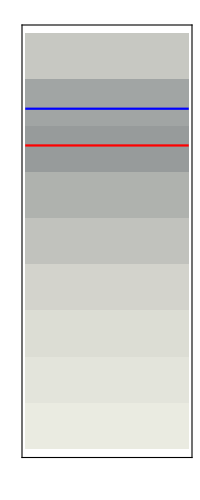

```mathematica
statDistPlot=Show[{MatrixPlot[0.5-Transpose[{Reverse[statDist[test]]}],Frame->True,FrameTicks->{False,False,{{nMax[test]+1,"0"},{nMax[test]-9,"10"},{nMax[test]-4,"5"},{1,ToString[nMax[test]]}},False},ColorFunction->"GrayTones"],ListLinePlot[{{0,statMean[test]},{1,statMean[test]}},PlotStyle->Red],ListLinePlot[{{0,n/.equi[[2]]/.test},{1,n/.equi[[2]]/.test}},PlotStyle->Blue]}]
```

# Density-independent Selection

## Evolution in an infinite population

```mathematica
ndi[i_]:=n[i](1+r0(1-(n[1]+n[2])/γ0))s[i];
```

```mathematica
Clear[Δn]
Δndi[i_]:=ndi[i]-n[i]
```

## Equilibria

```mathematica
equDI=Solve[{Δndi[1]==0,Δndi[2]==0},{n[1],n[2]}]/.{s[1]->s,s[2]->s-σ}
```

{{n[1]→0,n[2]→(γ0 (-1+s+r0 (s-σ)-σ))/(r0 (s-σ))},{n[1]→0,n[2]→0},{n[1]→((-1+s+r0 s) γ0)/(r0 s),n[2]→0}}

```mathematica
EquSubDetDI[pars_]:={n[1]->((-1+s+r0 s) γ0)/(r0 s),n[2]->0}/.pars;
```

```mathematica
nTotEquDetDI[pars_]:=(n[1]+n[2])/.EquSubDetDI[pars]
```

```mathematica
AFEquDetDI[pars_]:=(n[1]/(n[1]+n[2]))/.EquSubDetDI[pars]
```

## Numerical Dynamics

```mathematica
nDynDetDI[pars_,n0_,tmax_]:=Block[{out,t},out={Join[{0},n0]};
For[t=1,t≤tmax,t++,
AppendTo[out,{t,ndi[1],ndi[2]}/.{s[1]->s,s[2]->s-σ}/.pars/.{n[1]->out[[t,2]],n[2]->out[[t,3]]}]/.pars
];
out
]
```

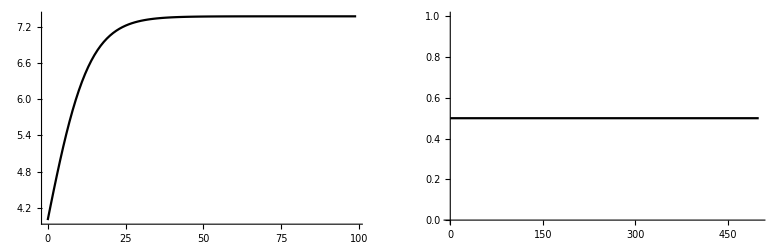

```mathematica
temp=nDynDetDI[test,{2,2},tmaxP];
GraphicsRow[{ListLinePlot[Transpose[{temp[[1;;tmaxN,1]],temp[[1;;tmaxN,2]]+temp[[1;;tmaxN,3]]}],PlotRange->All,PlotStyle->Black,ImageSize->Medium],ListLinePlot[Transpose[{temp[[;;,1]],temp[[;;,2]]/(temp[[;;,2]]+temp[[;;,3]])}],PlotRange->All,PlotStyle->Black,ImageSize->Medium]}]
```

## Evolution in a finite population

### Transition matrix

```mathematica
BMtrxDI[pars_]:=Block[{out,i1,j1,i2,j2,k,b1,b2,λ1,λ2},out={};
out=Table[0,{j,1,(nMax[pars])^2},{i,1,(nMax[pars])^2}];
For[i1=1,i1≤ nMax[pars],++i1,
For[i2=1,i2 ≤ nMax[pars],++i2,
λ1=i1 r0(1-(i1+i2)/γ0)/.pars;λ2=i2 r0(1-(i1+i2)/γ0)/.pars;
(*Print[{i1,i2,λ1,λ2}];*)
If[i1+i2<γ0/.pars,
For[j1=i1,j1≤nMax[pars],++j1,
For[j2=i2,j2≤nMax[pars],++j2,
b1=PDF[TruncatedDistribution[{-1,Max[nMax[pars]-i1-i2,0]},PoissonDistribution[λ1]],j1-i1];
b2=PDF[TruncatedDistribution[{-1,Max[nMax[pars]-i1-i2,0]},PoissonDistribution[λ2]],j2-i2];
out[[e[j1,j2,pars],e[i1,i2,pars]]]=b1 b2/.pars
]];];]];
For[k=1,k≤nMax[pars]^2,++k,
out[[k,k]]+=1-Total[out[[;;,k]]];
];
out
]
```

```mathematica
DMtrxDI[pars_]:=Block[{out,i1,j1,i2,j2},out={};
out=Table[0,{j,1,nMax[pars]^2},{i,1,nMax[pars]^2}];
For[i1=1,i1 ≤ nMax[pars],++i1,
For[i2=1,i2 ≤ nMax[pars],++i2,
For[j1=0,j1≤ nMax[pars],++j1,
For[j2=0,j2≤ nMax[pars],++j2,
If[j1≤i1&&j2≤i2,
out[[e[Max[j1,1],Max[j2,1],pars],e[i1,i2,pars]]]+=PDF[BinomialDistribution[i1,s],j1]PDF[BinomialDistribution[i2,s-σ],j2]/.pars
]
]];
]];
out//Chop
]
```

```mathematica
Clear[TMtrxDI]
TMtrxDI[pars_]:=TMtrxDI[pars]=DMtrxDI[pars].BMtrxDI[pars]//Chop
```

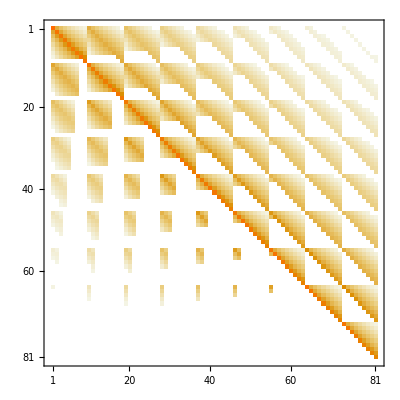

```mathematica
MatrixPlot[TMtrxDI[test]]
```

### Stochastic dynamics

#### Functions

The state of the stochastic process

```mathematica
stateDI[pars_,t_,n0_]:=stateDI[pars,t,n0]=v2m[pars,MatrixPower[TMtrxDI[pars],t].vec0[pars,n0]]
```

Distribution of the total population size at time t

```mathematica
nTotDynDistDI[pars_,t_,n0_]:=Block[{out,x},out={};
For[x=2,x≤nMax[pars],x++,
AppendTo[out,Sum[stateDI[pars,t,n0][[i,x-i]],{i,1,x-1}]]
];
out
]
```

the mean of the distribution of n Total at time t

```mathematica
nTotDynMeanDI[pars_,t_,n0_]:=Block[{out,i,j},
out=0;
For[i=1,i≤nMax[pars],i++,
For[j=1,j≤nMax[pars],j++,
out+=(i+j)stateDI[pars,t,n0][[i,j]]
];
];
out
]
```

The allele frequency distribution bined into multiples of 1/bin bins

```mathematica
AFDynDistDI[pars_,t_,n0_,bin_]:=Block[{out,i,j},
out=Table[0,{i,1,bin+1}];
For[i=1,i≤nMax[pars],i++,
For[j=1,j≤nMax[pars],j++,
out[[Round[i/(i+j),1/bin]*(bin)+1]]+=stateDI[pars,t,n0][[i,j]];  
]];
out 
]
```

```mathematica
AFDynMeanDI[pars_,t_,n0_]:=Block[{out,i,j},
out = 0;
For[i=1,i≤nMax[pars],i++,
For[j=1,j≤nMax[pars],j++,
out +=(i/(i+j))stateDI[pars,t,n0][[i,j]];
];
];
out
]
```

#### Dynamics Plots

```mathematica
nTotDynDistPlotDI[pars_,n0_]:=MatrixPlot[Transpose[Table[0.5-Reverse[nTotDynDistDI[pars,t,n0]],{t,0,tmaxN,ΔtN}]],ColorFunction->"GrayTones"];
```

```mathematica
nTotDynMeanPlotDI[pars_,n0_]:=ListLinePlot[Table[{t/ΔtN,nTotDynMeanDI[pars,t,n0]},{t,0,tmaxN,ΔtN}],PlotRange->All,PlotStyle->Red];
```

```mathematica
nTotDetDynPlotDI[pars_,n0_]:=Block[{temp},
temp=nDynDetDI[pars,n0,tmaxP];
ListLinePlot[Table[{i/ΔtN,(temp[[i+1,2]]+temp[[i+1,3]])},{i,0,tmaxN,ΔtN}],PlotRange->All,PlotStyle->Blue]
]
```

```mathematica
AFDynDistPlotDI[pars_,n0_]:=MatrixPlot[Transpose[Table[0.5-Reverse[AFDynDistDI[pars,t,n0,10]],{t,0,tmaxP,ΔtP}]],PlotRange->{{0,10},{0,tmaxP/ΔtP}},AspectRatio->0.5, ColorFunction->"GrayTones"];
```

```mathematica
AFDynMeanPlotDI[pars_,n0_]:=ListLinePlot[Table[{t/ΔtP,10 AFDynMeanDI[pars,t,n0]},{t,0,tmaxP,ΔtP}],PlotStyle->Red,PlotRange->All];
```

```mathematica
AFDetDynPlotDI[pars_,n0_]:=Block[{temp},
temp=nDynDetDI[pars,n0,tmaxP];
ListLinePlot[Table[{i/ΔtP,temp[[i+1,2]]/(temp[[i+1,2]]+temp[[i+1,3]])10},{i,0,tmaxP,ΔtP}],PlotRange->All,PlotStyle->Blue]
]
```

#### Combined Plots

```mathematica
nTotDynPlotDI[pars_,n0_]:=Show[{nTotDynDistPlotDI[pars,n0],nTotDynMeanPlotDI[pars,n0],nTotDetDynPlotDI[pars,n0]},FrameTicks->{Table[{t/ΔtN+1,ToString[t]},{t,0,tmaxN,ΔtN*10}],Table[{i,ToString[i]},{i,1,nMax[pars],3}],False,False}]
```

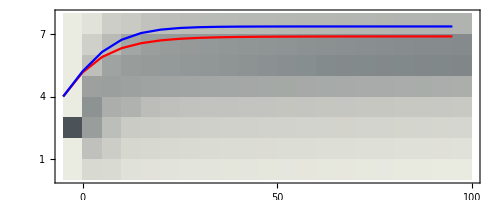

```mathematica
nTotDynPlotDI[test,{2,2}]
```

```mathematica
AFDynPlotDI[pars_,n0_]:=Show[{AFDynDistPlotDI[pars,n0],AFDynMeanPlotDI[pars,n0],AFDetDynPlotDI[pars,n0]},FrameTicks->{Table[{t/ΔtP+1,ToString[t]},{t,0,tmaxP,10*ΔtP}],Table[{i,ToString[N[i/10]]},{i,1,10,2}],False,False}]
```

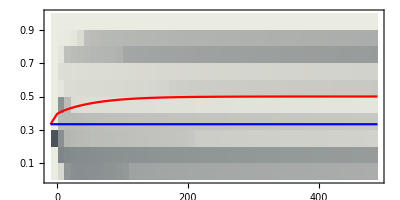

```mathematica
AFDynPlotDI[test,{1,2}]
```

### Stationary distribution

#### Calculating Stationary Distribution

```mathematica
Clear[equs,vars]
equs[pars_]:=Join[Table[(TMtrxDI[pars][[2;;,2;;]].Table[Π[i],{i,2,nMax[pars]^2}])[[j-1]]+Π[1] TMtrxDI[pars][[j-1,1]]==Π[j],{j,2,(nMax[pars])^2}],{Total[Table[Π[i],{i,2,(nMax[pars])^2}]]==1-Π[1]}]
vars[pars_]:=Table[Π[i],{i,1,(nMax[pars])^2}]
```

```mathematica
Clear[statDistDI]
statDistDI[pars_]:=statDistDI[pars]=Table[Π[i],{i,1,(nMax[pars])^2}]/.Flatten[Chop[NSolve[equs[pars],vars[pars]]]]
```

```mathematica
temp=v2m[test,statDistDI[test]];
```

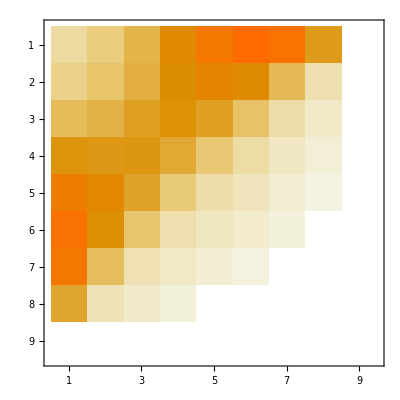

```mathematica
temp//MatrixPlot
```

```mathematica
temp[[1,6]]
```

0.0595096

```mathematica
temp[[6,1]]
```

0.0540067

#### Functions

```mathematica
nTotStatDistDI[pars_]:=Block[{statM,i,j,out},out=Table[0,{i,2,2nMax[pars]}];
statM=v2m[pars,statDistDI[pars]];
For[i=1,i≤nMax[pars],i++,
For[j=1,j≤nMax[pars],j++,
out[[i+j-1]]+=statM[[i,j]]
];
];
out
]
```

```mathematica
nTotStatMeanDI[pars_]:=nTotStatDistDI[pars].Table[i,{i,2,2nMax[pars]}];
```

```mathematica
AFStatDistDI[pars_,bin_]:=Block[{statM,i,j,out},out=Table[0,{i,1,10}];
statM=v2m[pars,statDistDI[pars]];
For[i=1,i≤nMax[pars],i++,
For[j=1,j≤nMax[pars],j++,
out[[Round[i/(i+j),1/bin]*(bin)+1]]+=statM[[i,j]]
];
];
out
]
```

```mathematica
AFStatMeanDI[pars_]:=Block[{statM,i,j,out},out=0;
statM=v2m[pars,statDistDI[pars]];
For[i=1,i≤nMax[pars],i++,
For[j=1,j≤nMax[pars],j++,
out+=i/(i+j)statM[[i,j]]
];
];
out
]
```

#### Plots

```mathematica
nTotStatDistPlotDI[pars_]:=MatrixPlot[Transpose[{0.5-Reverse[nTotStatDistDI[pars][[1;;nMax[pars]]]]}],ColorFunction->"GrayTones"];
```

```mathematica
nTotStatMeanPlotDI[pars_]:=ListLinePlot[{{0,nTotStatMeanDI[pars]},{1,nTotStatMeanDI[pars]}},PlotStyle->Red,PlotRange->{1,nMax[pars]+1}];
```

```mathematica
nTotEquPlotDI[pars_]:=ListLinePlot[{{0,(n[1]+n[2])/.EquSubDetDI[pars]},{1,(n[1]+n[2])/.EquSubDetDI[pars]}},PlotStyle->Blue,PlotRange->{1,nMax[pars]+1}];
```

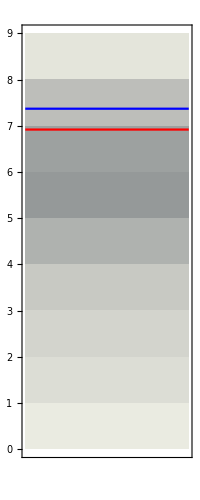

```mathematica
Show[{nTotStatDistPlotDI[test],nTotStatMeanPlotDI[test],nTotEquPlotDI[test]},FrameTicks->{False,Table[{i,ToString[i]},{i,0,nMax[test]}],False,False}]
```

```mathematica
AFStatDistPlotDI[pars_]:=MatrixPlot[Transpose[{Reverse[0.5-AFStatDistDI[pars,10]]}],ColorFunction->"GrayTones"];
```

```mathematica
AFStatMeanPlotDI[pars_]:=ListLinePlot[{{0,10AFStatMeanDI[pars]},{1,10AFStatMeanDI[pars]}},PlotStyle->Red,PlotRange->{0,10}];
```

```mathematica
AFEquPlotDI[pars_]:=ListLinePlot[{{0,(n[1]/(n[1]+n[2])10)/.EquSubDetDI[pars]},{1,(n[1]/(n[1]+n[2])10)/.EquSubDetDI[pars]}},PlotStyle->Blue,PlotRange->{1,nMax[pars]+1}];
```

```mathematica
AFStatMeanDI[{r0->0.2,γ0->2,s->0.9,σ->0.0,β->1}]
```

0.359944

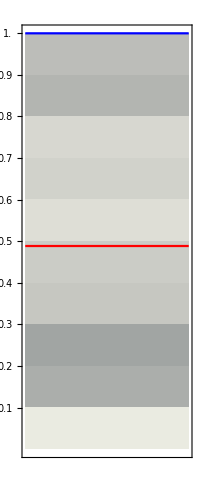

```mathematica
Show[{AFStatDistPlotDI[test],AFStatMeanPlotDI[test],AFEquPlotDI[test]},FrameTicks->{False,Table[{i,ToString[N[i/10]]},{i,1,10}],False,False}]
```

## Finite vs. Infinite population

### N-Total

```mathematica
nTotComp[γ0in_,βin_]:=Block[{out,PARS},
PARS={r0->0.2,γ0->γ0in,s->0.9,σ->0.0,β->βin};
out={γ0in,βin,nTotEquDetDI[PARS],nTotStatMeanDI[PARS]}
]
```

```mathematica
temp0=Table[nTotComp[γ,0.05],{γ,4,20,2}];
```

```mathematica
temp1=Table[nTotComp[γ,0.5],{γ,4,20,2}];
```

```mathematica
temp2=Table[nTotComp[γ,5],{γ,4,20,2}];
```

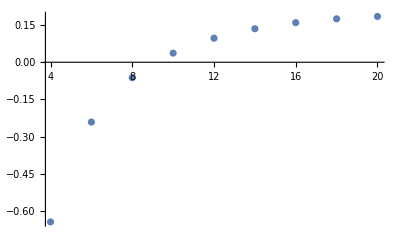

```mathematica
ListPlot[{Transpose[{temp0[[;;,1]],(temp0[[;;,3]]-temp0[[;;,4]])/temp0[[;;,3]]}](*,Transpose[{temp1[[;;,1]],(temp1[[;;,3]]-temp1[[;;,4]])/temp1[[;;,3]]}],Transpose[{temp2[[;;,1]],(temp2[[;;,3]]-temp2[[;;,4]])/temp2[[;;,3]]}]*)},PlotRange->All]
```

### Allele Frequency

```mathematica
AFComp[γ0in_,βin_]:=Block[{out,PARS},
PARS={r0->0.2,γ0->γ0in,s->0.9,σ->0.0,β->βin};
out={γ0in,βin,AFEquDetDI[PARS],AFStatMeanDI[PARS]}
]
```

```mathematica
temp0=Table[AFComp[γ,0.05],{γ,4,20,2}];
```

```mathematica
temp1=Table[AFComp[γ,0.5],{γ,4,20,2}];
```

```mathematica
temp2=Table[AFComp[γ,5],{γ,4,20,2}];
```

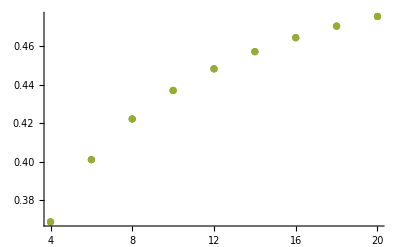

```mathematica
ListPlot[{Transpose[{temp0[[;;,1]],temp0[[;;,4]]}],Transpose[{temp1[[;;,1]],temp1[[;;,4]]}],Transpose[{temp2[[;;,1]],temp2[[;;,4]]}]},PlotRange->All]
```

# Density-dependent Selection

## Constraints on r and k

```mathematica
n2dd[i_]:=n[i](1+r[i](1-(n[1]+n[2])/γ[i]))s+m/2;
```

```mathematica
Δndd[i_]:=n2dd[i]-n[i]
```

We can define a trade-off such that r[i]γ[i]^(1/β)=constant.  If we have a baseline genotype i=0 with growth rate of r[0] and growth limit of γ[0] then a genotype i with a growth rate r[i] must have a growth limit of:

```mathematica
Solve[{r0 γ0^(1/β)==r[i] γ[i]^(1/β)},γ[i]]//Simplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{γ[i]→((r0 γ0^(1/β))/r[i])^β}}

```mathematica
Clear[tOffSub]
```

```mathematica
tOffSub[i_]:={γ[i]->γ0(r0/r[i])^β/.{r[1]->r0,r[2]->r0+σ},r[1]->r0,r[2]->r0+σ};
```

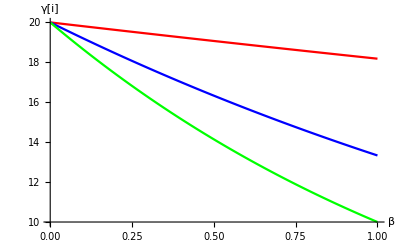

```mathematica
Plot[{γ[0]/.{r0->0.1,γ0->20,r[i]->0.2},γ0(r0/r[i])^β/.{r0->0.1,γ0->20,r[i]->0.11},γ0(r0/r[i])^β/.{r0->0.1,γ0->20,r[i]->0.15},γ0(r0/r[i])^β/.{r0->0.1,γ0->20,r[i]->0.2}},{β,0.001,1},PlotStyle->{{Black,Dashed},{Red},{Blue},{Green}},AxesLabel->{"β","γ[i]"}]
```

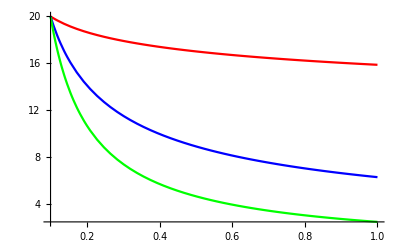

```mathematica
tradeOffPlot=Plot[{γ0(r0/x)^β/.{r0->0.1,γ0->20,β->0.1},γ0(r0/x)^β/.{r0->0.1,γ0->20,β->0.5},γ0(r0/x)^β/.{r0->0.1,γ0->20,β->0.9}},{x,0.1,1},PlotRange->All,PlotStyle->{Red,Blue,Green}]
```

```mathematica
(*Export["/Users/ailenemacpherson/Documents/Output/tradeoff.gif",tradeOffPlot,ImageResolution->700]*)
```

## Evolution in an infinite population

```mathematica
ndd[i_]:=n[i](1+r[i](1-(n[1]+n[2])/γ[i]))s/.tOffSub[i];
```

```mathematica
Δndd[i_]:=ndd[i]-n[i]
```

## Equilibria

```mathematica
equDD=Solve[{Δndd[1]==0,Δndd[2]==0},{n[1],n[2]}]
```

{{n[1]→0,n[2]→0},{n[1]→((-1+s+r0 s) γ0)/(r0 s),n[2]→0},{n[1]→0,n[2]→(γ0 (r0/(r0+σ))^β (-1+s+r0 s+s σ))/(s (r0+σ))}}

```mathematica
EquSubDetDD[pars_]:={n[1]->((-1+s+r0 s) γ0)/(r0 s),n[2]->0}/.pars;
```

```mathematica
nTotEquDetDD[pars_]:=(n[1]+n[2])/.EquSubDetDD[pars]
```

```mathematica
AFEquDetDD[pars_]:=(n[1]/(n[1]+n[2]))/.EquSubDetDD[pars]
```

## Numerical Dynamics

```mathematica
nDynDetDD[pars_,n0_,tmax_]:=Block[{out,t},out={Join[{0},n0]};
For[t=1,t≤tmax,t++,
AppendTo[out,{t,ndd[1],ndd[2]}/.{r[1]->r0,r[2]->r0+σ}/.pars/.{n[1]->out[[t,2]],n[2]->out[[t,3]]}]/.pars
];
out
]
```

```mathematica
temp=nDynDetDD[test,{2,2},tmaxP];
GraphicsRow[{ListLinePlot[Transpose[{temp[[1;;tmaxN,1]],temp[[1;;tmaxN,2]]+temp[[1;;tmaxN,3]]}],PlotRange->All,PlotStyle->Black,ImageSize->Medium],ListLinePlot[Transpose[{temp[[;;,1]],temp[[;;,2]]/(temp[[;;,2]]+temp[[;;,3]])}],PlotRange->All,PlotStyle->Black,ImageSize->Medium]}]
```

-Graphics-

## Evolution in a finite population

### Transition matrix

```mathematica
BMtrxDD[pars_]:=Block[{out,i1,j1,i2,j2,k,k2,b1,b2,λ1,λ2,temp},out={};
out=Table[0,{j,1,(nMax[pars])^2},{i,1,(nMax[pars])^2}];
For[i1=1,i1≤ nMax[pars],++i1,
For[i2=1,i2 ≤ nMax[pars],++i2,
λ1=i1 r[1](1-(i1+i2)/γ[1])/.tOffSub[1]/.{r[1]->r0}/.pars;λ2=i2 r[2](1-(i1+i2)/γ[2])/.tOffSub[2]/.{r[2]->r0+σ}/.pars;
(*Print[{i1,i2,λ1,λ2}];*)
For[j1=i1,j1≤nMax[pars],++j1,
For[j2=i2,j2≤nMax[pars],++j2,
b1=If[λ1>0/.pars,PDF[TruncatedDistribution[{-1,Max[nMax[pars]-i1-i2,0]},PoissonDistribution[λ1]],j1-i1],0];
b2=If[λ2>0/.pars,PDF[TruncatedDistribution[{-1,Max[nMax[pars]-i1-i2,0]},PoissonDistribution[λ2]],j2-i2],0];
out[[e[j1,j2,pars],e[i1,i2,pars]]]=b1 b2/.pars;
]];
]];
For[k=1,k≤nMax[pars]^2,++k,
out[[k,k]]+=1-Total[out[[;;,k]]]
];
out
]
```

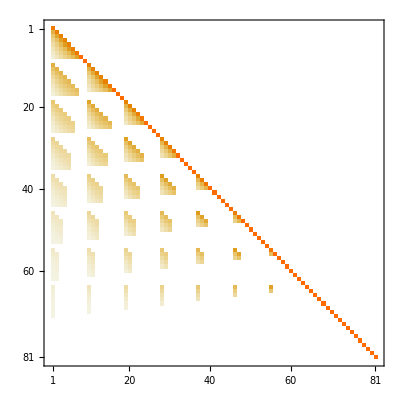

```mathematica
BMtrxDD[test]//MatrixPlot
```

```mathematica
DMtrxDD[pars_]:=Block[{out,i1,j1,i2,j2},out={};
out=Table[0,{j,1,nMax[pars]^2},{i,1,nMax[pars]^2}];
For[i1=1,i1 ≤ nMax[pars],++i1,
For[i2=1,i2 ≤ nMax[pars],++i2,
For[j1=0,j1≤ nMax[pars],++j1,
For[j2=0,j2≤ nMax[pars],++j2,
If[j1≤i1&&j2≤i2,
out[[e[Max[j1,1],Max[j2,1],pars],e[i1,i2,pars]]]+=PDF[BinomialDistribution[i1,s],j1]PDF[BinomialDistribution[i2,s-σ],j2]/.pars
]
]];
]];
out//Chop
]
```

```mathematica
Clear[TMtrxDD]
TMtrxDD[pars_]:=TMtrxDD[pars]=DMtrxDD[pars].BMtrxDD[pars]//Chop
```

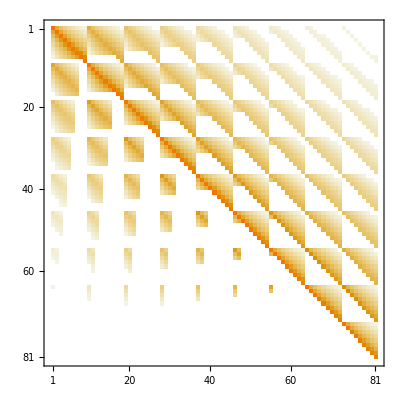

```mathematica
MatrixPlot[TMtrxDD[test]]
```

### Stochastic dynamics

#### Functions

The state of the stochastic process

```mathematica
Clear[stateDD]
stateDD[pars_,t_,n0_]:=stateDD[pars,t,n0]=v2m[pars,MatrixPower[TMtrxDD[pars],t].vec0[pars,n0]]
```

Distribution of the total population size at time t

```mathematica
nTotDynDistDD[pars_,t_,n0_]:=Block[{out,x},out={};
For[x=2,x≤nMax[pars],x++,
AppendTo[out,Sum[stateDD[pars,t,n0][[i,x-i]],{i,1,x-1}]]
];
out
]
```

the mean of the distribution of n Total at time t

```mathematica
nTotDynMeanDD[pars_,t_,n0_]:=Block[{out,i,j},
out=0;
For[i=1,i≤nMax[pars],i++,
For[j=1,j≤nMax[pars],j++,
out+=(i+j)stateDD[pars,t,n0][[i,j]]
];
];
out
]
```

The allele frequency distribution binned into multiples of 1/bin bins

```mathematica
AFDynDistDD[pars_,t_,n0_,bin_]:=Block[{out,i,j},
out=Table[0,{i,1,bin+1}];
For[i=1,i≤nMax[pars],i++,
For[j=1,j≤nMax[pars],j++,
out[[Round[i/(i+j),1/bin]*(bin)+1]]+=stateDD[pars,t,n0][[i,j]];  
]];
out 
]
```

```mathematica
AFDynMeanDD[pars_,t_,n0_]:=Block[{out,i,j},
out = 0;
For[i=1,i≤nMax[pars],i++,
For[j=1,j≤nMax[pars],j++,
out +=(i/(i+j))stateDD[pars,t,n0][[i,j]];
];
];
out
]
```

#### Dynamics Plots

```mathematica
nTotDynDistPlotDD[pars_,n0_]:=MatrixPlot[Transpose[Table[0.5-Reverse[nTotDynDistDD[pars,t,n0]],{t,0,tmaxN,ΔtN}]],ColorFunction->"GrayTones"];
```

```mathematica
nTotDynMeanPlotDD[pars_,n0_]:=ListLinePlot[Table[{t/ΔtN,nTotDynMeanDD[pars,t,n0]},{t,0,tmaxN,ΔtN}],PlotRange->All,PlotStyle->Red];
```

```mathematica
nTotDetDynPlotDD[pars_,n0_]:=Block[{temp},
temp=nDynDetDD[pars,n0,tmaxP];
ListLinePlot[Table[{i/ΔtN,(temp[[i+1,2]]+temp[[i+1,3]])},{i,0,tmaxN,ΔtN}],PlotRange->All,PlotStyle->Blue]
]
```

```mathematica
AFDynDistPlotDD[pars_,n0_]:=MatrixPlot[Transpose[Table[0.5-Reverse[AFDynDistDD[pars,t,n0,10]],{t,0,tmaxP,ΔtP}]],PlotRange->{{0,10},{0,tmaxP/ΔtP}},AspectRatio->0.5, ColorFunction->"GrayTones"];
```

```mathematica
AFDynMeanPlotDD[pars_,n0_]:=ListLinePlot[Table[{t/ΔtP,10 AFDynMeanDD[pars,t,n0]},{t,0,tmaxP,ΔtP}],PlotStyle->Red,PlotRange->All];
```

```mathematica
AFDetDynPlotDD[pars_,n0_]:=Block[{temp},
temp=nDynDetDD[pars,n0,tmaxP];
ListLinePlot[Table[{i/ΔtP,temp[[i+1,2]]/(temp[[i+1,2]]+temp[[i+1,3]])10},{i,0,tmaxP,ΔtP}],PlotRange->All,PlotStyle->Blue]
]
```

#### Combined Plots

```mathematica
nTotDynPlotDD[pars_,n0_]:=Show[{nTotDynDistPlotDD[pars,n0],nTotDynMeanPlotDD[pars,n0],nTotDetDynPlotDD[pars,n0]},FrameTicks->{Table[{t/ΔtN+1,ToString[t]},{t,0,tmaxN,ΔtN*10}],Table[{i,ToString[i]},{i,1,nMax[pars],3}],False,False}]
```

```mathematica
nTotDynPlotDD[test,{2,2}]
```

-Graphics-

```mathematica
AFDynPlotDD[pars_,n0_]:=Show[{AFDynDistPlotDD[pars,n0],AFDynMeanPlotDD[pars,n0],AFDetDynPlotDD[pars,n0]},FrameTicks->{Table[{t/ΔtP+1,ToString[t]},{t,0,tmaxP,10*ΔtP}],Table[{i,ToString[N[i/10]]},{i,1,10,2}],False,False}]
```

```mathematica
AFDynPlotDD[test,{1,2}]
```

-Graphics-

### Stationary distribution

#### Calculating Stationary Distribution

```mathematica
Clear[equs,vars]
equs[pars_]:=Join[Table[(TMtrxDD[pars][[2;;,2;;]].Table[Π[i],{i,2,nMax[pars]^2}])[[j-1]]+Π[1] TMtrxDD[pars][[j-1,1]]==Π[j],{j,2,(nMax[pars])^2}],{Total[Table[Π[i],{i,2,(nMax[pars])^2}]]==1-Π[1]}]
vars[pars_]:=Table[Π[i],{i,1,(nMax[pars])^2}]
```

```mathematica
Clear[statDistDD]
statDistDD[pars_]:=statDistDD[pars]=Table[Π[i],{i,1,(nMax[pars])^2}]/.Flatten[Chop[NSolve[equs[pars],vars[pars]]]]
```

```mathematica
v2m[test,statDistDD[test]]//MatrixPlot
```

-Graphics-

#### Functions

```mathematica
nTotStatDistDD[pars_]:=Block[{statM,i,j,out},out=Table[0,{i,2,2nMax[pars]}];
statM=v2m[pars,statDistDD[pars]];
For[i=1,i≤nMax[pars],i++,
For[j=1,j≤nMax[pars],j++,
out[[i+j-1]]+=statM[[i,j]]
];
];
out
]
```

```mathematica
nTotStatMeanDD[pars_]:=nTotStatDistDD[pars].Table[i,{i,2,2nMax[pars]}];
```

```mathematica
AFStatDistDD[pars_,bin_]:=Block[{statM,i,j,out},out=Table[0,{i,1,10}];
statM=v2m[pars,statDistDD[pars]];
For[i=1,i≤nMax[pars],i++,
For[j=1,j≤nMax[pars],j++,
out[[Round[i/(i+j),1/bin]*(bin)+1]]+=statM[[i,j]]
];
];
out
]
```

```mathematica
AFStatMeanDD[pars_]:=Block[{statM,i,j,out},out=0;
statM=v2m[pars,statDistDD[pars]];
For[i=1,i≤nMax[pars],i++,
For[j=1,j≤nMax[pars],j++,
out+=i/(i+j)statM[[i,j]]
];
];
out
]
```

#### Plots

```mathematica
nTotStatDistPlotDD[pars_]:=MatrixPlot[Transpose[{0.5-Reverse[nTotStatDistDD[pars][[1;;nMax[pars]]]]}],ColorFunction->"GrayTones"];
```

```mathematica
nTotStatMeanPlotDD[pars_]:=ListLinePlot[{{0,nTotStatMeanDD[pars]},{1,nTotStatMeanDD[pars]}},PlotStyle->Red,PlotRange->{1,nMax[pars]+1}];
```

```mathematica
nTotEquPlotDD[pars_]:=ListLinePlot[{{0,(n[1]+n[2])/.EquSubDetDD[pars]},{1,(n[1]+n[2])/.EquSubDetDD[pars]}},PlotStyle->Blue,PlotRange->{1,nMax[pars]+1}];
```

```mathematica
Show[{nTotStatDistPlotDD[test],nTotStatMeanPlotDD[test],nTotEquPlotDD[test]},FrameTicks->{False,Table[{i,ToString[i]},{i,0,nMax[test]}],False,False}]
```

-Graphics-

```mathematica
AFStatDistPlotDD[pars_]:=MatrixPlot[Transpose[{Reverse[0.5-AFStatDistDD[pars,10]]}],ColorFunction->"GrayTones"];
```

```mathematica
AFStatMeanPlotDD[pars_]:=ListLinePlot[{{0,10AFStatMeanDD[pars]},{1,10AFStatMeanDD[pars]}},PlotStyle->Red,PlotRange->{0,10}];
```

```mathematica
AFEquPlotDD[pars_]:=ListLinePlot[{{0,(n[1]/(n[1]+n[2])10)/.EquSubDetDD[pars]},{1,(n[1]/(n[1]+n[2])10)/.EquSubDetDD[pars]}},PlotStyle->Blue,PlotRange->{1,nMax[pars]+1}];
```

```mathematica
Show[{AFStatDistPlotDD[test],AFStatMeanPlotDD[test],AFEquPlotDD[test]},FrameTicks->{False,Table[{i,ToString[N[i/10]]},{i,1,10}],False,False}]
```

-Graphics-

## Finite vs. Infinite population

### N-Total

```mathematica
nTotComp[γ0in_,βin_]:=Block[{out,PARS},
PARS={r0->0.2,γ0->γ0in,s->0.9,σ->0.0,β->βin};
out={γ0in,βin,nTotEquDetDD[PARS],nTotStatMeanDD[PARS]}
]
```

```mathematica
temp0=Table[nTotComp[γ,0.05],{γ,4,20,2}];
```

```mathematica
temp1=Table[nTotComp[γ,0.5],{γ,4,20,2}];
```

```mathematica
temp2=Table[nTotComp[γ,5],{γ,4,20,2}];
```

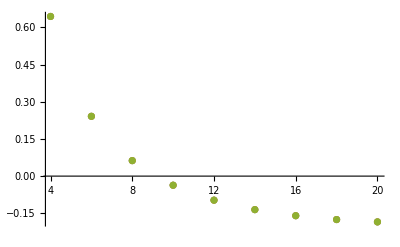

```mathematica
ListPlot[{Transpose[{temp0[[;;,1]],(temp0[[;;,4]]-temp0[[;;,3]])/temp0[[;;,3]]}],Transpose[{temp1[[;;,1]],(temp1[[;;,4]]-temp1[[;;,3]])/temp1[[;;,3]]}],Transpose[{temp2[[;;,1]],(temp2[[;;,4]]-temp2[[;;,3]])/temp2[[;;,3]]}]},PlotRange->All]
```

(Observed-Expected)/Expected

Why do I observe this pattern?  My guess: I think this might have to do with the boundaries on population size 0 and nMax=1.2*deterministic-expectation.  When population size is small the smallest population size in the stochastic model is 2 (1 individual of each type) whereas the maximum population size is nMax^2 which is much larger than the the deterministic population size 1/x nMax where x is the approximation factor.

### Allele Frequency

```mathematica
AFComp[γ0in_,βin_]:=Block[{out,PARS},
PARS={r0->0.2,γ0->γ0in,s->0.9,σ->0.0,β->βin};
out={γ0in,βin,AFEquDetDD[PARS],AFStatMeanDD[PARS]}
]
```

```mathematica
temp0=Table[AFComp[γ,0.05],{γ,4,20,2}];
```

```mathematica
temp1=Table[AFComp[γ,0.5],{γ,4,20,2}];
```

```mathematica
temp2=Table[AFComp[γ,5],{γ,4,20,2}];
```

```mathematica
ListPlot[{Transpose[{temp0[[;;,1]],temp0[[;;,4]]}],Transpose[{temp1[[;;,1]],temp1[[;;,4]]}],Transpose[{temp2[[;;,1]],temp2[[;;,4]]}]},PlotRange->All]
```

-Graphics-

Observed allele frequency as a function of gamma (population size).

Why do I have a non-0.5 allele frequency when gamma is small?  I would expect there to be more variation when populations are smaller but expectation should still be 0.5.  Maybe I am screwing something up when calculating the stationary distribution or perhaps something about the reflecting boundary and/or the birth approximation are harming this?